# Spring with drift

## Free-space solution starting at x0 > 0, traveling to the left at speed v.

```mathematica
p[x, t] = (Sqrt[C0/Pi]/A0)*Exp[-3*k*t/2]*Exp[-Exp[-3*k*t]*(C0/A0^2)*(x-x0+A0*Exp[k*t])^2]
```

(√C0 ⅇ^(-(3 k t)/2-(C0 ⅇ^(-3 k t) (A0 ⅇ^(k t)+x-x0)^2)/A0^2))/(A0 √π)

```mathematica
Integrate[p[x, t], {x, -Infinity, Infinity}]
```

ConditionalExpression[(√C0 ⅇ^(-(3 k t)/2))/(A0 √((C0 ⅇ^(-3 k t))/A0^2)),Re[(C0 ⅇ^(-3 k t))/A0^2]≥0]

```mathematica
Manipulate[Plot[(A0 ⅇ^((3 k t)/2) √((C0 ⅇ^(-3 k t))/A0^2) √π)/(√C0),{t,-8,8}],{A0,-8,8},{C0,-2,2},{k,-2,2}]
```

## Find absorption probability q(absorbed at t | survived until t)

```mathematica
q[t] =Normal @ FullSimplify[Integrate[p[x,t], {x, -Infinity, 0}]]
```

(A0 ⅇ^((3 k t)/2) √((C0 ⅇ^(-3 k t))/A0^2) (1+Erf[√((C0 ⅇ^(-3 k t))/A0^2) (A0 ⅇ^(k t)-x0)]))/(2 √C0)

```mathematica
q[t] = (1/2)*Erfc[√(C0/A0^2) (x0*ⅇ^(-3 k t/2)-A0 ⅇ^(-k t/2))]
```

1/2 Erfc[√(C0/A0^2) (-A0 ⅇ^(-(k t)/2)+ⅇ^(-(3 k t)/2) x0)]

```mathematica
Manipulate[Plot[1/2 Erfc[√(C0/A0^2) (-A0 ⅇ^(-(k t)/2)+ⅇ^(-(3 k t)/2) x0)],{t,0,20}, PlotRange->{0, 1}],{A0,1,10},{C0,1,10},{k,0.001,0.1},{x0,1,10}]
```

```mathematica
Manipulate[Plot[1/2 Erfc[√(C0/A0^2) (-A0*(1-k*t/2)+(1-3*k*t/2) *x0)],{t,0,20}, PlotRange->{0, 1}],{A0,1,10},{C0,1,10},{k,0.001,0.1},{x0,1,10}]
```

```mathematica
q[t] = (1/2)*Erfc[√(C0/A0^2) (-A0*(1-k*t/2)+(1-3*k*t/2) *x0)]
```

1/2 Erfc[√(C0/A0^2) (-A0 (1-(k t)/2)+(1-(3 k t)/2) x0)]

## Integrate to get survival probability from dS/S = -q(t) S(t)

```mathematica
lnS[t] = Simplify[-Integrate[q[t], t]]
```

-1/(2 A0^3 (C0/A0^2)^(3/2) k √π (A0-3 x0))(2 C0^(3/2) √π (A0-x0) Erf[(√C0 (A0 (-2+k t)+(2-3 k t) x0))/(2 A0)]+A0 C0 (-2 ⅇ^(-(C0 (A0 (-2+k t)+(2-3 k t) x0)^2)/(4 A0^2))+√(C0/A0^2) k √π t (A0-3 x0) Erfc[1/2 √(C0/A0^2) (A0 (-2+k t)+(2-3 k t) x0)]))

```mathematica
S[t] = Exp[%]
```

ⅇ^(-(2 C0^(3/2) √π (A0-x0) Erf[(√C0 (A0 (-2+k t)+(2-3 k t) x0))/(2 A0)]+A0 C0 (-2 ⅇ^(-(C0 (A0 (-2+k t)+(2-3 k t) x0)^2)/(4 A0^2))+√(C0/A0^2) k √π t (A0-3 x0) Erfc[1/2 √(C0/A0^2) (A0 (-2+k t)+(2-3 k t) x0)]))/(2 A0^3 (C0/A0^2)^(3/2) k √π (A0-3 x0)))

Apply initial condition

```mathematica
S[t] = S[t]*Exp[x0/(2*v)]
```

ⅇ^(-(ⅇ^(-(k (-t v+x0)^2)/(2 D)))/(√(k/D) √(2 π) v)+x0/(2 v)+(√D √(k/D) x0 Erf[(√k (t v-x0))/(√2 √D)])/(2 √k v)-1/2 t (1+Erf[(√(k/D) (t v-x0))/(√2)]))

## Get first-passage time probability

```mathematica
F[t] =S[t]*q[t]
```

1/2 ⅇ^(-(ⅇ^(-(k (-t v+x0)^2)/(2 D)))/(√(k/D) √(2 π) v)+x0/(2 v)+(√D √(k/D) x0 Erf[(√k (t v-x0))/(√2 √D)])/(2 √k v)-1/2 t (1+Erf[(√(k/D) (t v-x0))/(√2)])) (1+Erf[(√(k/D) (t v-x0))/(√2)])

```mathematica
f[t_, x0_, v_, D_, k_] =%
```

1/2 ⅇ^(-(ⅇ^(-(k (-t v+x0)^2)/(2 D)))/(√(k/D) √(2 π) v)+x0/(2 v)+(√D √(k/D) x0 Erf[(√k (t v-x0))/(√2 √D)])/(2 √k v)-1/2 t (1+Erf[(√(k/D) (t v-x0))/(√2)])) (1+Erf[(√(k/D) (t v-x0))/(√2)])

```mathematica
S[t_, x0_, A_, C0_, k_] = S[t]/.A0 -> SuperStar[A]-x0
```

ⅇ^(-(2 C0^(3/2) √π Erf[(√C0 ((2-3 k t) x0+(-2+k t) (-x0+A^*)))/(2 (-x0+A^*))] (-2 x0+A^*)+C0 (-x0+A^*) (-2 ⅇ^(-(C0 ((2-3 k t) x0+(-2+k t) (-x0+A^*))^2)/(4 (-x0+A^*)^2))+k √π t Erfc[1/2 √(C0/((-x0+A^*)^2)) ((2-3 k t) x0+(-2+k t) (-x0+A^*))] (-4 x0+A^*) √(C0/((-x0+A^*)^2))))/(2 k √π (-4 x0+A^*) (C0/((-x0+A^*)^2))^(3/2) (-x0+A^*)^3))

```mathematica
q[t_, x0_, v_, D_, k_] = q[t]
```

1/2 (1+Erf[(√(k/D) (t v-x0))/(√2)])

```mathematica
MaTeX["q(t)= \\frac{1}{2}\\text{erfc}\\left[\\sqrt{\\frac{\\kappa}{2D}}(x_0-vt)\\right]"]
```

-Graphics-

```mathematica
MaTeX["F(t)= \\frac{1}{2}\\text{erfc}\\left[\\sqrt{\\frac{\\kappa}{2D}}(x_0-vt)\\right] e^{\\displaystyle \\frac{1}{2v} (x_0-vt)\\text{erfc}{\\left(\\sqrt{\\frac{\\kappa}{2 D}} (x_0-vt)\\right)}}e^{\\displaystyle -\\frac{1}{v}\\sqrt{\\frac{D}{2 \\pi  \\kappa}} e^{-\\frac{\\kappa}{2D} (x_0-vt)^2}} "]
```

-Graphics-

## Plots and scaling

## Scaling with x0

```mathematica
x0Constant = 10
ARange = Range[11, 20, 1]
 C0Constant = 1
 kConstant = 0.01
```

10

{11,12,13,14,15,16,17,18,19,20}

1

0.01

### Plot survival probability S(t), Absorption probability q(t), and FPT F(t) = S(t)q(t)

```mathematica
Plot[Thread[S[t,x0Constant, ARange, C0Constant, kConstant]],{t,-1000,1000}, PlotRange->{0,1}]
(*Plot[Thread[q[t,x0Range, vConstant, DConstant, kConstant]],{t,-200,1000}, PlotRange->{0,1}]
Plot[Thread[f[t,x0Range, vConstant, DConstant, kConstant]],{t,-200,1000}, PlotRange->{0,0.01}]*)
```

-Graphics-

```mathematica
checkAreas = NIntegrate[f[t,x0Range, vConstant, DConstant, kConstant], {t, -1000, 1000}]
x0means = NIntegrate[t*f[t,x0Range, vConstant, DConstant, kConstant], {t, -1000, 1000}]
x0var = NIntegrate[t*t*f[t,x0Range, vConstant, DConstant, kConstant], {t, -1000, 1000}] - x0means^2
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{-112.209,-12.209,87.791,187.791,287.791,387.791,487.791,587.791,687.791,787.791}

{1925.51,1925.51,1925.51,1925.51,1925.51,1925.51,1925.51,1925.51,1925.51,1925.51}

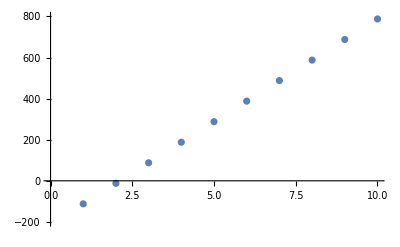

```mathematica
ListPlot[Thread[{x0Range, x0means}], PlotRange->{-200, 800}]
```

### Mean FPT scales linearly with x0.

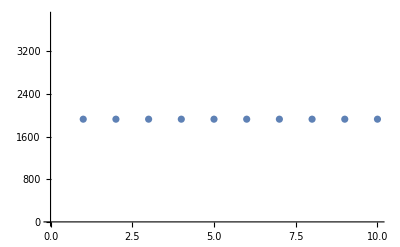

```mathematica
ListPlot[Thread[{x0Range, x0var}]]
```

### Variance of FPT does not scale with x0.

## Scaling with v

```mathematica
vRange = Range[0.001,0.02 , 0.001]
 DConstant = 1
 kConstant = 1
x0Constant = 10
```

{0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02}

1

1

10

### Plot survival probability, q(t), F(t) = S(t)q(t)

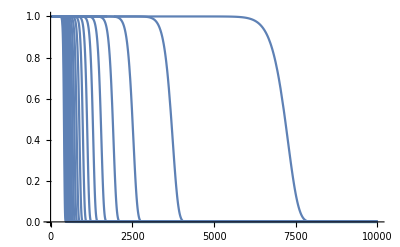

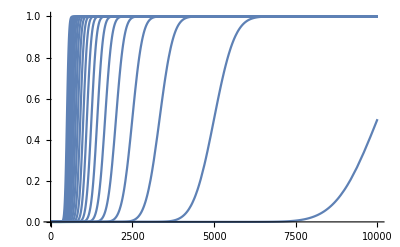

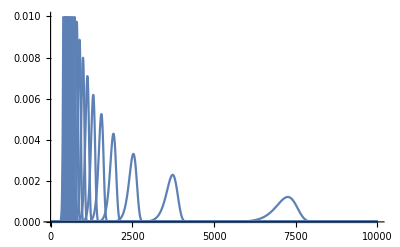

```mathematica
Plot[Thread[S[t,x0Constant, vRange, DConstant, kConstant]],{t,-1,10000}, PlotRange->{0,1}]
Plot[Thread[q[t,x0Constant, vRange, DConstant, kConstant]],{t,-1,10000}, PlotRange->{0,1}]
Plot[Thread[q[t,x0Constant, vRange, DConstant, kConstant]*S[t,x0Constant, vRange, DConstant, kConstant]],{t,-1,10000}, PlotRange->{0,0.01}]
```

```mathematica
vmeans = NIntegrate[t*f[t,x0Constant, vRange, DConstant, kConstant], {t, 0, 10000}]
vvar = NIntegrate[t*t*f[t,x0Constant, vRange, DConstant, kConstant], {t, 0, 10000}]  - vmeans^2
```

{7127.07,3668.45,2488.48,1889.89,1526.87,1282.78,1107.19,974.69,871.078,787.791,719.351,662.093,613.468,571.648,535.291,503.386,475.156,449.997,427.432,407.075}

{129936.,36044.2,17110.4,10111.2,6734.44,4837.08,3659.65,2876.,2326.56,1925.51,1623.22,1389.35,1204.42,1055.48,933.642,832.598,747.8,675.888,614.334,561.205}

{{0.001,7127.07},{0.002,3668.45},{0.003,2488.48},{0.004,1889.89},{0.005,1526.87},{0.006,1282.78},{0.007,1107.19},{0.008,974.69},{0.009,871.078},{0.01,787.791},{0.011,719.351},{0.012,662.093},{0.013,613.468},{0.014,571.648},{0.015,535.291},{0.016,503.386},{0.017,475.156},{0.018,449.997},{0.019,427.432},{0.02,407.075}}

{{0.001,129936.},{0.002,36044.2},{0.003,17110.4},{0.004,10111.2},{0.005,6734.44},{0.006,4837.08},{0.007,3659.65},{0.008,2876.},{0.009,2326.56},{0.01,1925.51},{0.011,1623.22},{0.012,1389.35},{0.013,1204.42},{0.014,1055.48},{0.015,933.642},{0.016,832.598},{0.017,747.8},{0.018,675.888},{0.019,614.334},{0.02,561.205}}

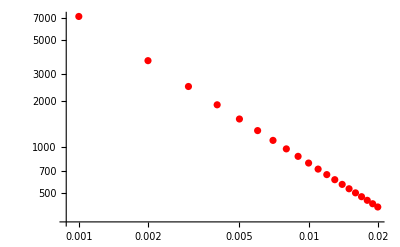

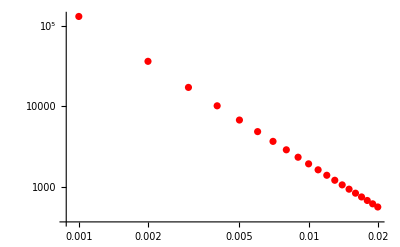

```mathematica
meandata = Thread[{vRange, vmeans}]
vardata = Thread[{vRange, vvar}] 
Show[ListLogLogPlot[meandata,PlotStyle->Red]]
Show[ListLogLogPlot[vardata,PlotStyle->Red]]
```

### Mean FPT scales with a negative power of v. However, it approaches a finite value (it seems like at a certain point, going faster doesn’t get you there faster)

### Variance FPT scales with a negative power of v.

## Scaling with D

```mathematica
vConstant = 0.01
 DRange = Range[0.1, 1, 0.1]
 kConstant = 1
x0Constant = 10
```

0.01

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

1

10

### Plot survival probability, q(t), F(t) = S(t)q(t)

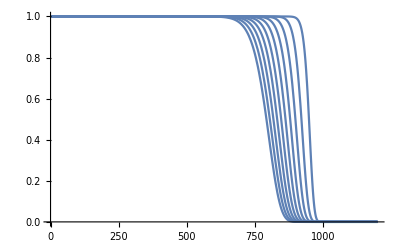

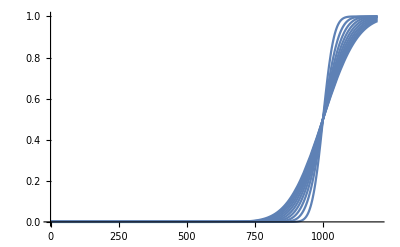

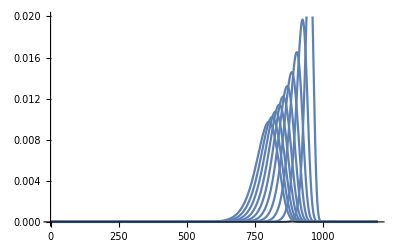

```mathematica
Plot[Thread[S[t,x0Constant, vConstant, DRange, kConstant]],{t,0,1200}, PlotRange->{0,1}]
Plot[Thread[q[t,x0Constant, vConstant, DRange, kConstant]],{t,0,1200}, PlotRange->{0,1}]
Plot[Thread[f[t,x0Constant, vConstant, DRange, kConstant]],{t,0,1200}, PlotRange->{0,0.02}]
```

```mathematica
Dmeans = NIntegrate[t*f[t,x0Constant, vConstant, DRange, kConstant], {t, -200, 1000}]
Dvar = NIntegrate[t*t*f[t,x0Constant, vConstant, DRange, kConstant], {t, -200, 1000}]  - Dmeans^2
```

{947.163,918.881,896.235,876.646,859.067,842.948,827.952,813.858,800.509,787.791}

{254.792,461.211,659.14,850.294,1036.68,1219.44,1399.27,1576.67,1751.99,1925.51}

{{0.1,947.163},{0.2,918.881},{0.3,896.235},{0.4,876.646},{0.5,859.067},{0.6,842.948},{0.7,827.952},{0.8,813.858},{0.9,800.509},{1.,787.791}}

{{0.1,254.792},{0.2,461.211},{0.3,659.14},{0.4,850.294},{0.5,1036.68},{0.6,1219.44},{0.7,1399.27},{0.8,1576.67},{0.9,1751.99},{1.,1925.51}}

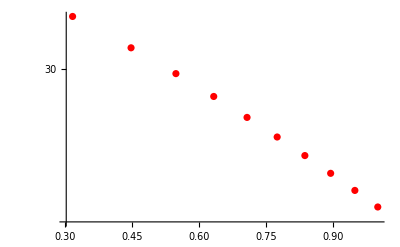

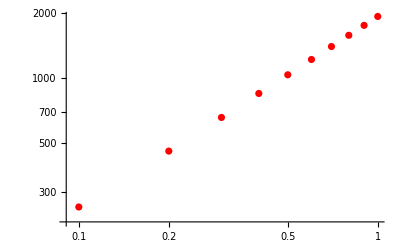

```mathematica
meandata = Thread[{DRange, Dmeans}]
vardata = Thread[{DRange, Dvar}]
Show[ListLogPlot[meandata^(1/2),PlotStyle->Red]]
Show[ListLogLogPlot[vardata,PlotStyle->Red]]
```

### Mean FPT scales with e^(-D^(1/2))

### Variance FPT scales with a positive power of D.

## Scaling with κ

```mathematica
vConstant = 0.01
 DConstant =1
 kRange =  Range[1, 10, 1]
x0Constant = 10
```

0.01

1

{1,2,3,4,5,6,7,8,9,10}

10

### Plot survival probability, q(t), F(t) = S(t)q(t)

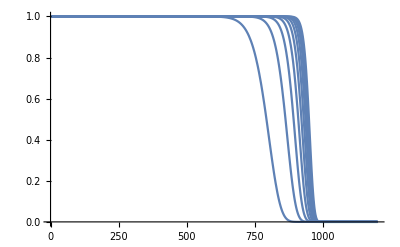

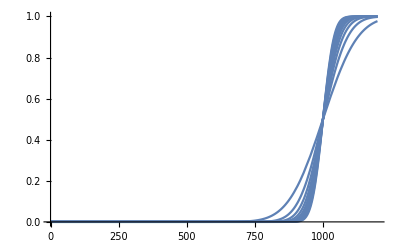

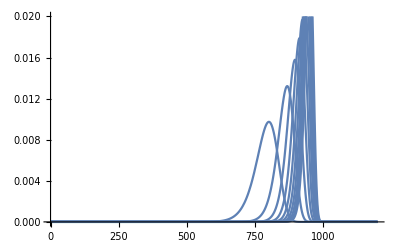

```mathematica
Plot[Thread[S[t,x0Constant, vConstant, DConstant, kRange]],{t,0,1200}, PlotRange->{0,1}]
Plot[Thread[q[t,x0Constant, vConstant, DConstant, kRange]],{t,0,1200}, PlotRange->{0,1}]
Plot[Thread[f[t,x0Constant, vConstant, DConstant, kRange]],{t,0,1200}, PlotRange->{0,0.02}]
```

```mathematica
kmeans = NIntegrate[t*f[t,x0Constant, vConstant, DConstant, kRange], {t, -200, 1000}]
kvar = NIntegrate[t*t*f[t,x0Constant, vConstant, DConstant, kRange], {t, -200, 1000}]  - kmeans^2
```

{787.791,859.067,889.433,907.075,918.881,927.459,934.035,939.273,943.566,947.163}

{1925.51,1036.68,723.484,561.207,461.211,393.136,343.748,306.397,277.442,254.792}

{{1,787.791},{2,859.067},{3,889.433},{4,907.075},{5,918.881},{6,927.459},{7,934.035},{8,939.273},{9,943.566},{10,947.163}}

{{1,1925.51},{2,1036.68},{3,723.484},{4,561.207},{5,461.211},{6,393.136},{7,343.748},{8,306.397},{9,277.442},{10,254.792}}

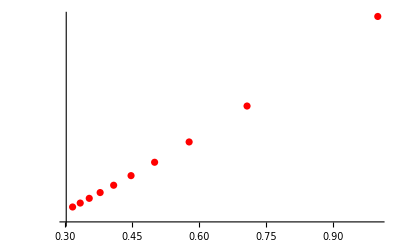

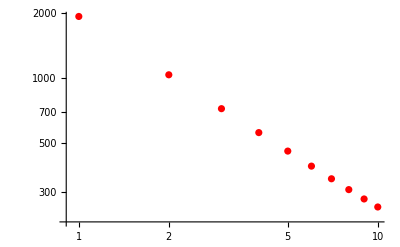

```mathematica
meandata = Thread[{kRange, kmeans}]
vardata = Thread[{kRange, kvar}]
Show[ListLogPlot[meandata^(-1/2),PlotStyle->Red]]
Show[ListLogLogPlot[vardata,PlotStyle->Red]]
```

### Mean FPT scales with e^(κ^(-1/2))

### Variance FPT scales with a negative power of κ.